```mathematica
Be=0.37h 100 c;
ωe=634 100 c 2 π;
c = 2.99792458*^8;
h = 6.62607004*^-34;
ℏ = h/(2π);
kb = 1.38064852*^-23;
T=4;
A=135*100 c;
vibMaxBoltz[v_,T_]:=(Exp[-ℏ ωe/(2kb T)](1-Exp[-ℏ ωe/(kb T)])^-1)^-1 Exp[-ℏ (ωe(v+1/2))/(kb T)]
MaxBoltz[v_,J_,T_]:=vibMaxBoltz[v,T]((2J+1)Exp[-(Be (J(J+1)))/(kb T)])/Sum[(2k+1)Exp[-(Be( k(k+1)))/(kb T)],{k,3/2,300+3/2}]
```

General::munfl: Exp[-709.187] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.751] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-748.581] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

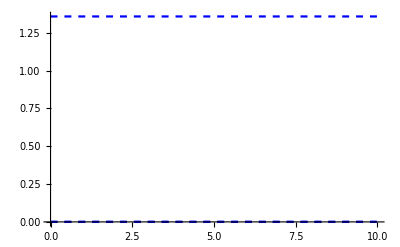

```mathematica
Plot[{Sum[MaxBoltz[0,k,T],{k,0,100}],Sum[MaxBoltz[2,k,T],{k,0,100}],Sum[MaxBoltz[1,k,T],{k,0,100}]},{t,0,10},PlotStyle->Table[{Blue,Dashed},{i,1,3}]]
```

```mathematica
MBrotPop=Table[MaxBoltz[0,J,T],{J,0,100}];
```

General::munfl: Exp[-709.187] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.751] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-748.581] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

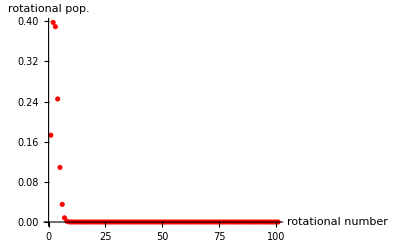

```mathematica
ListPlot[{MBrotPop},AxesLabel->{"rotational number","rotational pop."},PlotStyle->{Red,Dashed},PlotRange->All]
```

```mathematica
MaxBoltz[0,1.5,T]*1/(Exp[-h A/(kb T)]+1)
```

General::munfl: Exp[-709.187] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.751] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-748.581] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.419885

```mathematica
MaxBoltz[0,2.5,T]*1/(Exp[-h A/(kb T)]+1)
```

General::munfl: Exp[-709.187] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.751] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-748.581] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.323763

```mathematica
MaxBoltz[0,3.5,T]*1/(Exp[-h A/(kb T)]+1)
```

General::munfl: Exp[-709.187] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.751] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-748.581] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.170049

```mathematica
MaxBoltz[0,4.5,T]*1/(Exp[-h A/(kb T)]+1)
```

General::munfl: Exp[-709.187] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.751] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-748.581] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.0641643

```mathematica
Elec=1/(Exp[-h A/(kb T)]+1)
```

1.

```mathematica
kb T
```

5.52259×10^-23

```mathematica
ℏ (2π*A)/(kb T)
```

48.5587

```mathematica
A
```

4.0472×10^12